I.1 x-πy+5^(1/3)z=0 is a linear equation
I.2 x^2+y^2+z^2=1 is NOT a linear equation
I.3 x^-1+7y+z=(Sin[π/9])^2 is NOT a linear equation
I.4 x+7y+z=Sin[π/9] is a linear equation
I.5 3Cos[x]-4y+z=√3 is NOT a linear equation
I.6 Cos[3]x-4y+z=√3 is a linear equation

II.7

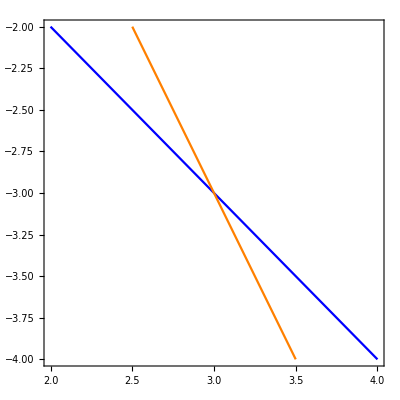

{{x→3,y→-3}}

```mathematica
ContourPlot[{x + y == 0, 2*x + y == 3}, {x, 2, 4}, {y, -4, -2},ContourStyle->{Blue,Orange}]
(*
Piecewise[{{x+y, =0}, {2x+y, =3}}]⇒({{1, 1, 0}, {2, 1, 3}})⇒Subscript[R, 2]-2 Subscript[R, 1]⇒({{1, 1, 0}, {0, -1, 3}})⇒Piecewise[{{x+y, =0}, {-y, =3}}]
y=-3

x+y=0
x=-(-3)
x=3
*)
Solve[{x + y == 0,2*x + y == 3}, {x,y}]
```

II.8

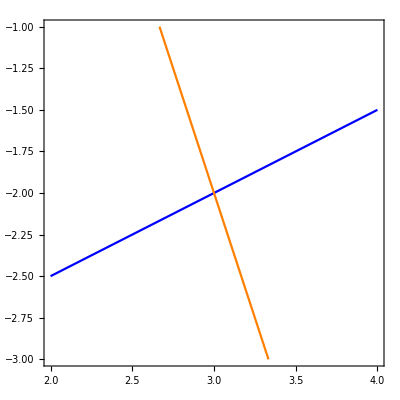

{{x→3,y→-2}}

```mathematica
ContourPlot[{x - 2*y == 7, 3*x + y == 7}, {x, 2, 4}, {y, -3, -1},ContourStyle->{Blue,Orange}]
(*
Piecewise[{{x-2y, =7}, {3x+y, =7}}]⇒({{1, -2, 7}, {3, 1, 7}})⇒Subscript[R, 2]-3 Subscript[R, 1]⇒({{1, -2, 7}, {0, 7, -14}})⇒Piecewise[{{x-2y, =7}, {7y, =-14}}]
y=-2

x-2y=7
x=7+2(-2)
x=3
*)
Solve[{x - 2*y == 7,3*x + y == 7}, {x,y}]
```

II.9

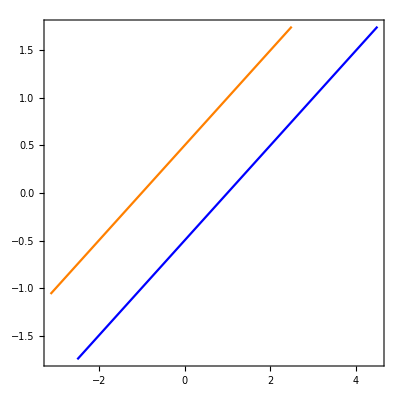

{}

```mathematica
ContourPlot[{3*x - 6*y == 3, -x + 2*y == 1}, {x, -3.125, 4.5}, {y, -1.75, 1.75},ContourStyle->{Blue,Orange}]
(*
Piecewise[{{3x-6y, =3}, {-x+2y, =1}}]⇒({{3, -6, 3}, {-1, 2, 1}})⇒Subscript[R, 2]+1/3 Subscript[R, 1]⇒({{3, -6, 3}, {0, 0, 2}})⇒Piecewise[{{3x-6y, =3}, {0, =2}}]
no solution
*)
Solve[{ 3*x - 6*y == 3,  -x + 2*y == 1}, {x,y}]
```

```mathematica
VIII
Piecewise[{{kx+y, =-2}, {2x-2y, =4}}]⇒({{k, 1, -2}, {2, -2, 4}})⇒1/k Subscript[R, 1]⇒({{1, 1/k, -2/k}, {2, -2, 4}})⇒Subscript[R, 2]-2 Subscript[R, 1]⇒({{1, 1/k, -2/k}, {0, -(2 (1+k))/k, 4+4/k}})⇒-k/(2 (1+k))Subscript[R, 2]⇒({{1, 1/k, -2/k}, {0, 1, -2}})⇒Subscript[R, 1]-1/k Subscript[R, 2]⇒({{1, 0, 0}, {0, 1, -2}})
{{x=0}, {y=-2; for all k}}
```

```mathematica
A=({{k, 1, -2}, {2, -2, 4}});
RowReduce[A];
MatrixForm[%]
Solve[{k*x+y==-2,2x-2y==4},{x,y}]
xMin=-3;
xMax=2;
ContourPlot3D[{k*x+y==-2,2x-2y==4},{x,xMin,xMax},{y,xMin,xMax},{k,xMin,xMax},Axes->True,AxesLabel->{x,y,z},PlotLegends->"Expressions"]
```

(1 | 0 | 0
0 | 1 | -2)

{{x→0,y→-2}}

-Graphics3D-

Optional 1
Consider the following matrix
A=(π | π | π
π^2 | π^2 | π^2
π^3 | π^3 | π^3)
1. Find the reduced row echelon from of A; then find the rank of A.
2. How can you enter in Mathenatica (in one line) the matrix A? (without typing every entry!). Hint: Consider the Table command.
3. Now generalize the result as follows: let X be the following arbitrary square matrix of size n, where c is any non-zero number. Compute the rank of X.
X=(c | c | ⋯ | c
c^2 | c^2 | ⋯ | c^2
⋮ | ⋮ | ⋮ | ⋮
c^n | c^n | ⋯ | c^n)

Optional 1.1

```mathematica
A=({{π, π, π}, {π^2, π^2, π^2}, {π^3, π^3, π^3}});
Print["RowReduce[A]=" MatrixForm[RowReduce[A]]]
Print["MatrixRank[A]="]
MatrixRank[A]
```

RowReduce[A]= (1 | 1 | 1
0 | 0 | 0
0 | 0 | 0)

MatrixRank[A]=

1

Optional 1.2

```mathematica
A=Table[Pi^i,{i,1,3},{j,1,3}];
MatrixForm[A]
```

(π | π | π
π^2 | π^2 | π^2
π^3 | π^3 | π^3)

Optional 1.3
X=(c | c | ⋯ | c
c^2 | c^2 | ⋯ | c^2
⋮ | ⋮ | ⋮ | ⋮
c^n | c^n | ⋯ | c^n)⇒ 1/X_11 R_1→R_1
1/X_21 R_2→R_2
⋮
1/X_n1 R_n→R_n⇒ (1 | 1 | ⋯ | 1
1 | 1 | ⋯ | 1
⋮ | ⋮ | ⋮ | ⋮
1 | 1 | ⋯ | 1)⇒  R_2-R_1→R_2
R_3-R_1→R_3
⋮
R_n-R_1→R_n⇒ (1 | 1 | ⋯ | 1
0 | 0 | ⋯ | 0
⋮ | ⋮ | ⋮ | ⋮
0 | 0 | ⋯ | 0)

Optional 2
For what value(s) of k, if any, will the following system:
Piecewise[{{x+y+kz, =1}, {x+ky+z, =1}, {kx+y+z, =-2}}]
have
1. No solution
2. A unique solution
3. Infinitely many solutions
Hint. Find the reduced echelon form of the augmented matrix, then analyze different cases (beware of division by zero!).

Piecewise[{{x+y+kz, =1}, {x+ky+z, =1}, {kx+y+z, =-2}}]⇒ (1 | 1 | k | 1
1 | k | 1 | 1
k | 1 | 1 | -2)⇒ R_1↔R_3⇒ (k | 1 | 1 | -2
1 | k | 1 | 1
1 | 1 | k | 1)⇒ 1/k R_1→R_1⇒ (1 | 1/k | 1/k | -2/k
1 | k | 1 | 1
1 | 1 | k | 1)⇒ R_2-R_1→R_2
R_3-R_1→R_3⇒ (1 | 1/k | 1/k | -2/k
0 | k-1/k | 1-1/k | 1+2/k
0 | 1-1/k | k-1/k | 1+2/k)⇒ R_1-1/(-1+k^2)R_2→R_1⇒ (1 | 0 | 1/(1+k) | (1+2k)/(1-k^2)
0 | k-1/k | 1-1/k | 1+2/k
0 | 1-1/k | k-1/k | 1+2/k)⇒ k/(-1+k^2)R_2→R_2⇒ (1 | 0 | 1/(1+k) | (1+2k)/(1-k^2)
0 | 1 | 1/(1+k) | (2+k)/(-1+k^2)
0 | 1-1/k | k-1/k | 1+2/k)⇒ R_3-(1-1/k)R_2→R_3⇒ (1 | 0 | 1/(1+k) | (1+2k)/(1-k^2)
0 | 1 | 1/(1+k) | (2+k)/(-1+k^2)
0 | 0 | k-2/(1+k) | 1+1/(1+k))⇒ (1+k)/(-2+k+k^2)R_3→R_3⇒ (1 | 0 | 1/(1+k) | (1+2k)/(1-k^2)
0 | 1 | 1/(1+k) | (2+k)/(-1+k^2)
0 | 0 | 1 | 1/(-1+k))⇒ R_2-1/(1+k)R_3→R_2
R_1-1/(1+k)R_3→R_1⇒ (1 | 0 | 0 | -2/(-1+k)
0 | 1 | 0 | 1/(-1+k)
0 | 0 | 1 | 1/(-1+k))
z=1/(-1+k)
y=1/(-1+k)
x=-2/(-1+k)

Optional 2.1
The system does not have a solution for k = 1.

Optional 2.2 & 2.3
Since y = z, the system does not have a unique solution. Therefore the system has infinitely many solutions for k ≠ 1.

```mathematica
A=({{1, 1, k, 1}, {1, k, 1, 1}, {k, 1, 1, -2}});
RowReduce[A];
MatrixForm[%]
Solve[{x+y+k*z==1,x+k*y+z==1,k*x+y+z==-2},{x,y,z}]
```

(1 | 0 | 0 | -2/(-1+k)
0 | 1 | 0 | 1/(-1+k)
0 | 0 | 1 | 1/(-1+k))

{{x→-2/(-1+k),y→1/(-1+k),z→1/(-1+k)}}